```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/duff/Dropbox/DGLAP_MC/MC/Library/Test_Compile

```mathematica
(***********************************************************************************************)
(***********************************************************************************************)
(***********************************************************************************************)
(***********************************************************************************************)
(***********************************************************************************************)
(***********************************************************************************************)
(***********************************************************************************************)
(***********************************************************************************************)
(***********************************************************************************************)
```

```mathematica
SplitG[Z_,CA_,NF_]:=2CA(Z/(1-Z)+(1-Z)/Z+Z(1-Z))+NF/2(Z^2+(1-Z)^2)
```

```mathematica
PgTOggMomentStart=Integrate[SplitG[Z,CA,0]Z^(n-1),{Z,0,1},GenerateConditions->False];
PgTOqqbarMomentStart=Integrate[SplitG[Z,0,nf]Z^(n-1),{Z,0,1},GenerateConditions->False];

PqTOqgMomentStart=Integrate[CF((1+(1-Z)^2)/Z)Z^(n-1),{Z,0,1},GenerateConditions->False];

PqTOgqMomentStart=Integrate[CF((1+(Z)^2)/(1-Z))(Z)^(n-1),{Z,0,1},GenerateConditions->False];

β0alt[CA_,nf_]:=11/3 CA-4/3(1/2)nf;
```

```mathematica
FullSimplify[PqTOqgMomentStart/PqTOgqMomentStart]
```

-(2+n+n^2)/(n (-1+n^2) (EulerGamma+HarmonicNumber[1+n]+PolyGamma[0,n]))

```mathematica
PggMoment[CA_,nf_,n_]:=-2*CA*((1+n*(-1+2*n))/(n-n^3)+HarmonicNumber[2+n])+(β0alt[CA,nf])/2
```

```mathematica
PqTOgqMomentStart//InputForm
PqqMoment[CF_,n_]:=-(CF*(EulerGamma+HarmonicNumber[1+n]+PolyGamma[0,n]))-(-(CF*(EulerGamma+HarmonicNumber[1+n]+PolyGamma[0,n]))/.n->1)
```

-(CF*(EulerGamma + HarmonicNumber[1 + n] + PolyGamma[0, n]))

```mathematica
PgTOqqbarMomentStart//InputForm
PqgMoment[n_]:=((2+n+n^2))/(2*n*(1+n)*(2+n))
```

((2 + n + n^2)*nf)/(2*n*(1 + n)*(2 + n))

```mathematica
PqTOqgMomentStart//InputForm
PgqMoment[CF_,n_]:=(CF*(2+n+n^2))/(n*(-1+n^2))
```

(CF*(2 + n + n^2))/(n*(-1 + n^2))

```mathematica
PqqMoment[CF,n]
```

(3 CF)/2-CF (EulerGamma+HarmonicNumber[1+n]+PolyGamma[0,n])

```mathematica
Integrate[CF((1+(Z)^2)/(1-Z))-2/(1-Z),{Z,0,1},GenerateConditions->False]
```

-(3 CF)/2

```mathematica
PMomentrulesForSingletAnomDim[CA_,CF_,nf_,n_]:={Pgg->PggMoment[CA,nf,n],Pqg-> PqgMoment[n],Pgq-> PgqMoment[CF,n],Pqq->PqqMoment[CF,n]};
```

```mathematica
(***********************************************************************************************)
(***********************************************************************************************)
(***********************************************************************************************)
```

```mathematica
IDmatrix={{1,0},{0,1}};
```

```mathematica
NF1=2nf;NF2=1;NF3=1;
```

```mathematica
SingletEvoMatrix={{Pqq,NF1  Pgq},{NF2 Pqg,Pgg}}
```

{{Pqq,2 nf Pgq},{Pqg,Pgg}}

```mathematica
SingletEigenvalues=λ/.Simplify[Solve[Det[SingletEvoMatrix - λ {{1, 0}, {0, 1}}]==0,λ]];
```

```mathematica
SingletEigenvalues
```

{1/2 (Pgg+Pqq-√(Pgg^2+8 nf Pgq Pqg-2 Pgg Pqq+Pqq^2)),1/2 (Pgg+Pqq+√(Pgg^2+8 nf Pgq Pqg-2 Pgg Pqq+Pqq^2))}

```mathematica
SingletEigenvectorN={ NF3 A,B}/.Solve[Simplify[SingletEvoMatrix.{NF3 A,B}-SingletEigenvalues[[1]]{NF3 A,B}]==0,{A,B}][[1]]/.A->NormN;
SingletEigenvectorP={NF3 A,B}/.Solve[Simplify[SingletEvoMatrix.{NF3 A,B}-SingletEigenvalues[[2]]{NF3 A,B}]==0,{A,B}][[1]]/.A->NormP;
SingletEigenvectorNnormed=FullSimplify[SingletEigenvectorN/.PowerExpand[FullSimplify[Solve[(SingletEigenvectorN.SingletEigenvectorN)==1,NormN][[2]]]]];
SingletEigenvectorPnormed=FullSimplify[SingletEigenvectorP/.PowerExpand[FullSimplify[Solve[(SingletEigenvectorP.SingletEigenvectorP)==1,NormP][[2]]]]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
PositveProjectorSingletStart=SingletEvoMatrix-SingletEigenvalues[[1]]IDmatrix;
NegativeProjectorSingletStart=SingletEvoMatrix-SingletEigenvalues[[2]]IDmatrix;
```

```mathematica
PositveProjectorSinglet=PositveProjectorSingletStart/FullSimplify[Simplify[PositveProjectorSingletStart.SingletEigenvectorP]/SingletEigenvectorP][[1]];
NegativeProjectorSinglet=NegativeProjectorSingletStart/FullSimplify[Simplify[NegativeProjectorSingletStart.SingletEigenvectorN]/SingletEigenvectorN][[1]];
Simplify[PositveProjectorSinglet.SingletEigenvectorN]
Simplify[NegativeProjectorSinglet.SingletEigenvectorP]
```

{0,0}

{0,0}

```mathematica
PositveProjectorSingletEvolved=PositveProjectorSinglet Exp[t*SingletEigenvalues[[2]]];
NegativeProjectorSingletEvolved=NegativeProjectorSinglet Exp[t*SingletEigenvalues[[1]]];
```

```mathematica
EvolveLL=PositveProjectorSingletEvolved.{2nf A,B}+NegativeProjectorSingletEvolved.{2nf A,B};
```

```mathematica
EvolveLLGluon=EvolveLL[[2]];
EvolveLLQS=EvolveLL[[1]];
```

```mathematica
(***********************************************************************************************)
(***********************************************************************************************)
(***********************************************************************************************)
```

```mathematica
mZ=91.87;αsZ=0.1187;
αs[μ_]:=(1/αsZ+ β0alt[3,5]/(2π)Log[μ/mZ] )^-1
```

```mathematica
αsTest=Integrate[αs[μ]/μ,{μ,μI,μF},GenerateConditions->False]/π;
```

```mathematica
αsTest//InputForm
```

(0.8195459096321198*Log[2.3839717979164545 + 1.*Log[μF]] - 0.8195459096321198*Log[2.3839717979164545 + 1.*Log[μI]])/Pi

```mathematica
T[μI_,μF_]:=(6.283185307179586*Log[53.24733311169141-4.512912343060295*β0alt[3.,5.]+1.*Log[μF]*β0alt[3.,5.]]-6.283185307179586*Log[53.24733311169141-4.512912343060295*β0alt[3.,5.]+1.*Log[μI]*β0alt[3.,5.]])/(Pi*β0alt[3.,5.])
```

```mathematica
SUMRule[a1_,n_]:=(1/2)Sum[a1[[i,1]]^(n) a1[[i,2]](a1[[i+1,1]]-a1[[i,1]]),{i,1,Length[a1]-1}]+(1/2)Sum[a1[[i,1]]^(n) a1[[i,2]](a1[[i,1]]-a1[[i-1,1]]),{i,2,Length[a1]}]
```

```mathematica
(***********************************************************************************************)
(***********************************************************************************************)
(***********************************************************************************************)
```

```mathematica
EvolvedQSToJetQCD=EvolveLLQS+0EvolveLLGluon/.B->1/.A->1/.PMomentrulesForSingletAnomDim[3,4/3,5,n]/.nf->5;
EvolvedGToJetQCD=0EvolveLLQS+EvolveLLGluon/.A->1/.B->1/.PMomentrulesForSingletAnomDim[3,4/3,5,n]/.nf->5;
```

```mathematica
RealAxisIntercept=4;Clear[EvolvedGToJetQCDMomentum,EvolvedQSToJetQCDMomentum]
EvolvedGToJetQCDMomentum[x_,Thet_,η_]:=NIntegrate[1/π Im[Exp[I η] x^(-(RealAxisIntercept-0+r Exp[I η]))EvolvedGToJetQCD/.n->(RealAxisIntercept+r Exp[I η])/.t->Thet],{r,0,Infinity},PrecisionGoal->3,AccuracyGoal->3,MinRecursion->2];
EvolvedQSToJetQCDMomentum[x_,Thet_,η_]:=NIntegrate[1/π Im[Exp[I η] x^(-(RealAxisIntercept-0+r Exp[I η]))EvolvedQSToJetQCD/.n->(RealAxisIntercept+r Exp[I η])/.t->Thet],{r,0,Infinity},PrecisionGoal->3,AccuracyGoal->3,MinRecursion->2];
```

```mathematica
(***********************************************************************************************)
(***********************************************************************************************)
(***********************************************************************************************)
```

```mathematica
PlotStyle1={Purple,Orange,Darker[Green],Brown,Pink,Darker[Cyan],Darker[Red],Darker[Yellow],Red};
PlotStyle2={Directive[Dotted,Purple],Directive[Dotted,Orange],Directive[Dotted,Darker[Green]],Directive[Dotted,Brown],Directive[Dotted,Pink],Directive[Dotted,Darker[Cyan]],Directive[Dotted,Darker[Red]],Directive[Dotted,Darker[Yellow]],Directive[Dotted,Red]};
```

```mathematica
PlotStyle3={Directive[Dotted,Darker[Red]],Directive[Dotted,Darker[Green]],Directive[Dotted,Darker[Cyan]],Directive[Dotted,Darker[Yellow]]};
```

```mathematica
DoReimanIntegral[expr_]:=Sum[expr[[i,2]](expr[[i+1,1]]-expr[[i,1]]),{i,1,Length[expr]-1}]/2+Sum[expr[[i,2]](expr[[i,1]]-expr[[i-1,1]]),{i,2,Length[expr]}]/2
```

```mathematica
PruneBottom[expr_,bottom_]:=Complement[Table[If[(expr[[i,1]]/.nan->0)>bottom,expr[[i]]/.nan->0,BLAH],{i,1,Length[expr]}],{BLAH}];
PruneTop[expr_,top_]:=Complement[Table[If[(expr[[i,1]]/.nan->0)<top,expr[[i]]/.nan->0,BLAH],{i,1,Length[expr]}],{BLAH}];
```

```mathematica
TakeRatio[a1_,a2_]:=Table[{a1[[i,1]],a1[[i,2]]/a2[[i,2]]},{i,1,Length[a1]}];
DoSum[a1_]:=Sum[a1[[i]],{i,1,Length[a1]}];
Cumulative[a1_]:=Table[{a1[[i,1]],Sum[a1[[j,2]](a1[[j,1]]-a1[[j-1,1]]),{j,2,i}]/2+Sum[a1[[j,2]](a1[[j+1,1]]-a1[[j,1]]),{j,1,i-1}]/2},{i,1,Length[a1]}]
Clear[TakeDifference]
TakeDifference[a1_,a2_]:=Table[{a1[[i,1]],a1[[i,2]]-a2[[i,2]]},{i,1,Length[a1]}];
DOAverage[TheList_]:=Module[{OutPut,TotalEvents},
TotalEvents=Sum[TheList[[i,1,1]],{i,1,Length[TheList]}];
OutPut=Sum[TheList[[i,1,1]]TheList[[i]],{i,1,Length[TheList]}]/TotalEvents;
OutPut
]
```

```mathematica
SUMRule[a1_,n_]:=(1)Sum[If[a1[[i,1]]≠0,a1[[i,1]]^(n) ,0]a1[[i,2]](a1[[i+1,1]]),{i,1,1}]+Sum[If[a1[[i,1]]≠0,a1[[i,1]]^(n) ,0] a1[[i,2]](a1[[i,1]]-a1[[i-1,1]]),{i,Length[a1],Length[a1]}]+(1/2)Sum[If[a1[[i,1]]≠0,a1[[i,1]]^(n) ,0]a1[[i,2]](a1[[i+1,1]]-a1[[i,1]]),{i,2,Length[a1]-1}]+(1/2)Sum[If[a1[[i,1]]≠0,a1[[i,1]]^(n) ,0] a1[[i,2]](a1[[i,1]]-a1[[i-1,1]]),{i,2,Length[a1]-1}]
```

```mathematica
SUMRuleWithCut[a1_,n_,Xmin_]:=(1/2)Sum[If[Xmin<a1[[i,1]],If[a1[[i,1]]≠0,a1[[i,1]]^(n) ,0] a1[[i,2]](a1[[i+1,1]]-a1[[i,1]]),0],{i,1,Length[a1]-1}]+(1/2)Sum[If[Xmin<a1[[i,1]],If[a1[[i,1]]≠0,a1[[i,1]]^(n) ,0] a1[[i,2]](a1[[i,1]]-a1[[i-1,1]]),0],{i,2,Length[a1]}]
```

```mathematica
SUMRuleWithMaxCut[a1_,n_,Xmax_]:=(1/2)Sum[If[Xmax>a1[[i,1]],If[a1[[i,1]]≠0,a1[[i,1]]^(n) ,0] a1[[i,2]](a1[[i+1,1]]-a1[[i,1]]),0],{i,1,Length[a1]-1}]+(1/2)Sum[If[Xmax>a1[[i,1]],If[a1[[i,1]]≠0,a1[[i,1]]^(n) ,0] a1[[i,2]](a1[[i,1]]-a1[[i-1,1]]),0],{i,2,Length[a1]}]
```

```mathematica
EnforceSumRule[expr_]:=Module[{OutPut,Norm,Inter},
Inter=expr/.nan->0/.{a1_,a2_}:>{a1,UnitStep[a2]a2};
Norm=SUMRule[Inter,1];
OutPut=Inter/.{a1_,a2_}->{a1,a2/Norm};
OutPut
]
```

```mathematica
DoDer[a1_]:=Table[{a1[[j,1]],(a1[[j+1,2]]-a1[[j,2]])/(a1[[j+1,1]]-a1[[j,1]])},{j,2,Length[a1]-1}];
```

```mathematica
DoNormalizeLogBinSpecial[Spectra_,Cut1_,Cut2_]:=Module[{TheNorm,OutPut,CutSpectra,TheEndPointWieght},
CutSpectra=PruneTop[Spectra,Cut2];
TheEndPointWieght=SUMRule[Spectra,0]-SUMRule[CutSpectra,0];
OutPut=PruneBottom[Spectra/.{a1_,a2_}->{a1, a2/TheEndPointWieght},Cut2]
];
```

```mathematica
DoNormalize[Spectra_]:=Module[{TheNorm,OutPut},
TheNorm=SUMRule[Spectra,1];
OutPut=Spectra/.{a1_,a2_}->{a1, a2/TheNorm}
];
```

```mathematica
DoNormalizeLogBin[Spectra_]:=Module[{TheNorm,OutPut,SpectraII},
SpectraII=PruneBottom[Spectra,0.00001];
TheNorm=SUMRule[SpectraII,0];
OutPut=Spectra/.{a1_,a2_}->{a1, a2/TheNorm}
];
```

```mathematica
SmoothBins[Spectra_]:=EnforceSumRule[MovingAverage[Spectra,3]];
```

```mathematica
DoBinNormalize[Spectra_]:=Module[{TheNorm,OutPut,SpectraII},
SmoothBins[Table[{Spectra[[i,1]],Spectra[[i,2]]/(Spectra[[i+1,1]]-Spectra[[i,1]])},{i,1,Length[Spectra]-1}]]
];
```

```mathematica
CombineSpectra[LogBin_,RegBin_,Cut1_,Cut2_]:=Module[{GetNormLogBin,GetNormRegBin,CombinedSpectra},
GetNormLogBin=NIntegrate[Interpolation[LogBin][x],{x,.1,.4}]/.3;
GetNormRegBin=NIntegrate[Interpolation[RegBin/.{a1_,a2_}->{a1,a1 a2}][x],{x,.1,.4}]/.3;
CombinedSpectra=MovingAverage[Union[PruneBottom[RegBin/.{a1_,a2_}->{a1,a2 a1/GetNormRegBin},.1],PruneTop[LogBin/.{a1_,a2_}->{a1,a2 /GetNormLogBin},.9]],2];
DoNormalizeLogBinSpecial[CombinedSpectra,Cut1,Cut2]
]
```

```mathematica
DoNormalizeInt[Spectra_]:=Module[{TheNorm,OutPut},
TheNorm=SUMRule[Table[Spectra[[i]],{i,2,Length[Spectra]}],0];
OutPut=Spectra/.{a1_,a2_}->{a1, a2/TheNorm}
];
```

```mathematica
(*********************************************************************************************)
(*********************************************************************************************)
(*********************************************************************************************)
(*********************************************************************************************)
(*********************************************************************************************)
(*********************************************************************************************)
```

```mathematica
RandSeedMax=1;
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/duff/Dropbox/DGLAP_MC/MC/Library/Test_Compile

```mathematica
QtoJetFragSpecLogBinClassicDGLAPQ91test=DOAverage[Table[(<<("./Test/InclusiveSpectraLogBin_rseed"<>ToString[100+i]<>"_Q91.000000_Rmax1.570800_ProgramMode0_Flavor1_Angle.txt")),{i,1,RandSeedMax}]/.a1_+a2_*e->a2*10^a1/.e->1];
QtoJetFragSpecClassicDGLAPQ91test=DOAverage[Table[(<<("./Test/InclusiveSpectra_rseed"<>ToString[100+i]<>"_Q91.000000_Rmax1.570800_ProgramMode0_Flavor1_Angle.txt")),{i,1,RandSeedMax}]/.a1_+a2_*e->a2*10^a1/.e->1];
QtotoJetLeadingSpecClassicDGLAPQ91test=DOAverage[Table[(<<("./Test/LeadingJetSpectra_rseed"<>ToString[100+i]<>"_Q91.000000_Rmax1.570800_ProgramMode0_Flavor1_Angle.txt")),{i,1,RandSeedMax}]/.a1_+a2_*e->a2*10^a1/.e->1];
```

```mathematica
GtoJetFragSpecLogBinClassicDGLAPQ91test=DOAverage[Table[(<<("./Test/InclusiveSpectraLogBin_rseed"<>ToString[100+i]<>"_Q91.000000_Rmax1.570800_ProgramMode0_Flavor0_Angle.txt")),{i,1,RandSeedMax}]/.a1_+a2_*e->a2*10^a1/.e->1];
GtoJetFragSpecClassicDGLAPQ91test=DOAverage[Table[(<<("./Test/InclusiveSpectra_rseed"<>ToString[100+i]<>"_Q91.000000_Rmax1.570800_ProgramMode0_Flavor0_Angle.txt")),{i,1,RandSeedMax}]/.a1_+a2_*e->a2*10^a1/.e->1];
GtotoJetLeadingSpecClassicDGLAPQ91test=DOAverage[Table[(<<("./Test/LeadingJetSpectra_rseed"<>ToString[100+i]<>"_Q91.000000_Rmax1.570800_ProgramMode0_Flavor0_Angle.txt")),{i,1,RandSeedMax}]/.a1_+a2_*e->a2*10^a1/.e->1];
```

```mathematica
Table[SUMRule[QtoJetFragSpecClassicDGLAPQ91test[[2,i,2]],1],{i,1,Length[QtoJetFragSpecClassicDGLAPQ91test[[2]]]}]
```

{0.147657,0.999315,0.999788,1.00126,1.00225,1.00351,1.00736,1.01444,1.03859,1.0939}

```mathematica
Table[SUMRule[QtoJetFragSpecLogBinClassicDGLAPQ91test[[2,i,2]],1],{i,1,Length[QtoJetFragSpecClassicDGLAPQ91test[[2]]]}]
```

{4.91517×10^-8,1.28475×10^-7,3.53581×10^-7,5.13618×10^-7,5.65916×10^-7,6.16397×10^-7,7.29107×10^-7,8.30218×10^-7,1.00419×10^-6,1.15946×10^-6}

```mathematica
T[μI_,μF_]
```

0.0415187 (6.28319 Log[18.6483+7.66667 Log[μF_]]-6.28319 Log[18.6483+7.66667 Log[μI_]])

```mathematica
JetRaddi=Table[QtoJetFragSpecClassicDGLAPQ91test[[2,i,1]],{i,1,Length[QtoJetFragSpecClassicDGLAPQ91test[[2]]]}];
```

```mathematica
(***************************************************************************************************)
(***************************************************************************************************)
(***************************************************************************************************)
```

```mathematica
(*
This the inclusive spectra of the energy distribution for q or g jets. x-axis is the energy fraction of the jet of radius R. y-axis is number of jets. note that the normalization is sensitive to the end-point z-->1. Compare analytic prediction.
*)
```

```mathematica
TheQ=91.0;
MellinQtoJetQ91=Table[Table[{x,EvolvedQSToJetQCDMomentum[x,T[TheQ Tan[JetRaddi[[i]]/2],TheQ],.75 π]},{x,.01,.999,.01/2}],{i,1,Length[JetRaddi]}];
MellinGtoJetQ91=Table[Table[{x,EvolvedGToJetQCDMomentum[x,T[TheQ Tan[JetRaddi[[i]]/2],TheQ],.75 π]},{x,.01,.999,.01/2}],{i,1,Length[JetRaddi]}];
```

0.999

```mathematica
CutEndPoint=.99;
```

```mathematica
MakeCompareQuarkLOPlot[THeI_]:=ListPlot[{SmoothBins[PruneTop[QtoJetFragSpecClassicDGLAPQ91test[[2,THeI,2]],CutEndPoint]],EnforceSumRule[PruneTop[MellinQtoJetQ91[[THeI]],CutEndPoint]]},PlotRange->{0,5},PlotStyle->PlotStyle1,PlotLegends->{"MC", "Mellin"},PlotLabel->"Tan[R/2]="<>ToString[Tan[JetRaddi[[THeI]]/2]],Joined->True]
```

```mathematica
MakeCompareGluonLOPlot[THeI_]:=ListPlot[{SmoothBins[PruneTop[GtoJetFragSpecClassicDGLAPQ91test[[2,THeI,2]],CutEndPoint]],EnforceSumRule[PruneTop[MellinGtoJetQ91[[THeI]],CutEndPoint]]},PlotRange->{0,5},PlotStyle->PlotStyle1,PlotLegends->{"MC", "Mellin"},PlotLabel->"Tan[R/2]="<>ToString[Tan[JetRaddi[[THeI]]/2]],Joined->True]
```

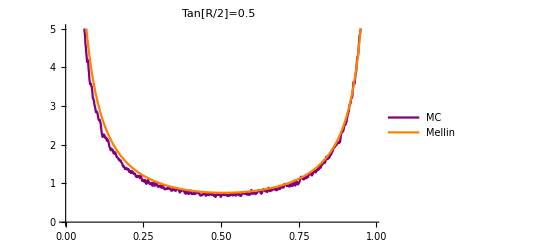

```mathematica
MakeCompareQuarkLOPlot[3]
```

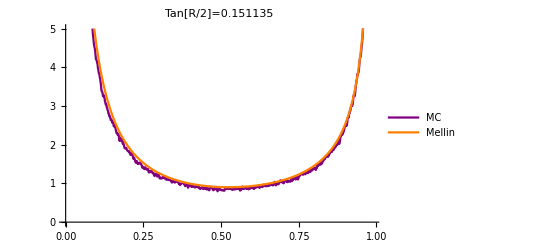

```mathematica
MakeCompareQuarkLOPlot[7]
```

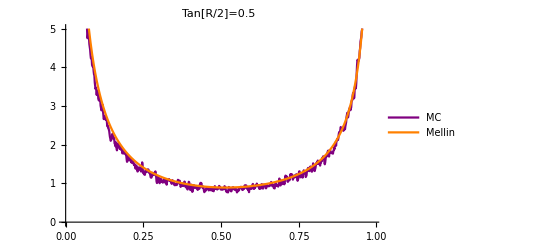

```mathematica
MakeCompareGluonLOPlot[3]
```

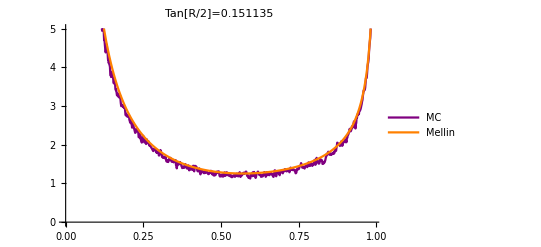

```mathematica
MakeCompareGluonLOPlot[7]
```

```mathematica
(***************************************************************************************************)
(***************************************************************************************************)
(***************************************************************************************************)
```

```mathematica
QktConserveClassicDGLAPQ91test=DOAverage[Table[(<<("./Test/KTconservation_rseed"<>ToString[100+i]<>"_Q91.000000_Rmax1.570800_ProgramMode0_Flavor1_Angle.txt")),{i,1,RandSeedMax}]/.a1_+a2_*e->a2*10^a1/.e->1];

GktConserveClassicDGLAPQ91test=DOAverage[Table[(<<("./Test/KTconservation_rseed"<>ToString[100+i]<>"_Q91.000000_Rmax1.570800_ProgramMode0_Flavor0_Angle.txt")),{i,1,RandSeedMax}]/.a1_+a2_*e->a2*10^a1/.e->1];
```

```mathematica
QktBroadeningClassicDGLAPQ91test=DOAverage[Table[(<<("./Test/KTBroadening_rseed"<>ToString[100+i]<>"_Q91.000000_Rmax1.570800_ProgramMode0_Flavor1_Angle.txt")),{i,1,RandSeedMax}]/.a1_+a2_*e->a2*10^a1/.e->1];

GktBroadeningClassicDGLAPQ91test=DOAverage[Table[(<<("./Test/KTBroadening_rseed"<>ToString[100+i]<>"_Q91.000000_Rmax1.570800_ProgramMode0_Flavor0_Angle.txt")),{i,1,RandSeedMax}]/.a1_+a2_*e->a2*10^a1/.e->1];
```

```mathematica
QThrustClassicDGLAPQ91test=DOAverage[Table[(<<("./Test/ThrustSpectra_rseed"<>ToString[100+i]<>"_Q91.000000_Rmax1.570800_ProgramMode0_Flavor1_Angle.txt")),{i,1,RandSeedMax}]/.a1_+a2_*e->a2*10^a1/.e->1];

GThrustClassicDGLAPQ91test=DOAverage[Table[(<<("./Test/ThrustSpectra_rseed"<>ToString[100+i]<>"_Q91.000000_Rmax1.570800_ProgramMode0_Flavor0_Angle.txt")),{i,1,RandSeedMax}]/.a1_+a2_*e->a2*10^a1/.e->1];
```

```mathematica
DaI=3
```

3

```mathematica
Sum[QktConserveClassicDGLAPQ91test[[2,DaI,2,i,1]],{i,1,Length[QktConserveClassicDGLAPQ91test[[2,DaI,2]]]}]
```

399.5

```mathematica
QktConserveClassicDGLAPQ91test[[2,DaI,2,2,1]]^-1
```

800.

```mathematica
QktConserveClassicDGLAPQ91test[[2,DaI,2,3,1]]-QktConserveClassicDGLAPQ91test[[2,DaI,2,2,1]]
QktConserveClassicDGLAPQ91test[[2,DaI,2,5,1]]-QktConserveClassicDGLAPQ91test[[2,DaI,2,4,1]]
```

0.00125

0.00125

```mathematica
Table[QktConserveClassicDGLAPQ91test[[2,i,2,2,2]],{i,1,Length[QktConserveClassicDGLAPQ91test[[2]]]}]/800
```

{0.980205,0.911369,0.809972,0.667337,0.60602,0.563594,0.488538,0.40678,0.293328,0.2087}

```mathematica
SUMRuleSpecial[a1_,n_]:=If[n==0,
a1[[2,2]](a1[[2,1]])+
Sum[If[a1[[i,1]]≠0,a1[[i,1]]^(n) ,0] a1[[i,2]](a1[[i,1]]-a1[[i-1,1]]),{i,Length[a1],Length[a1]}]+(1/2)Sum[If[a1[[i,1]]≠0,a1[[i,1]]^(n) ,0]a1[[i,2]](a1[[i+1,1]]-a1[[i,1]]),{i,3,Length[a1]-1}]+(1/2)Sum[If[a1[[i,1]]≠0,a1[[i,1]]^(n) ,0] a1[[i,2]](a1[[i,1]]-a1[[i-1,1]]),{i,3,Length[a1]-1}],

Sum[If[a1[[i,1]]≠0,a1[[i,1]]^(n) ,0] a1[[i,2]](a1[[i,1]]-a1[[i-1,1]]),{i,Length[a1],Length[a1]}]+(1/2)Sum[If[a1[[i,1]]≠0,a1[[i,1]]^(n) ,0]a1[[i,2]](a1[[i+1,1]]-a1[[i,1]]),{i,3,Length[a1]-1}]+(1/2)Sum[If[a1[[i,1]]≠0,a1[[i,1]]^(n) ,0] a1[[i,2]](a1[[i,1]]-a1[[i-1,1]]),{i,3,Length[a1]-1}]]
```

800.

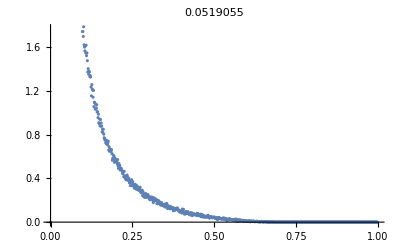

0.05

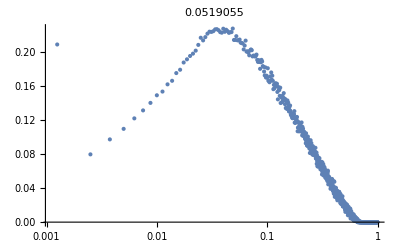

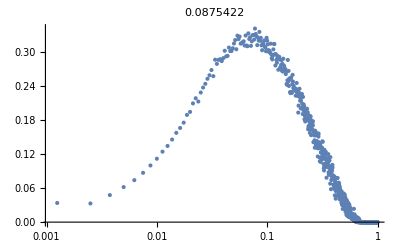

```mathematica
DaI=10;
Sum[QktConserveClassicDGLAPQ91test[[2,DaI,2,i,2]],{i,1,Length[QktConserveClassicDGLAPQ91test[[2,DaI,2]]]}]

ListPlot[QktConserveClassicDGLAPQ91test[[2,DaI,2]]/.{a1_,a2_}->{a1, a2},PlotLabel->ToString[SUMRule[QktConserveClassicDGLAPQ91test[[2,DaI,2]],1]]]
QktConserveClassicDGLAPQ91test[[2,DaI,1]]
ListLogLinearPlot[QktConserveClassicDGLAPQ91test[[2,DaI,2]]/.{a1_,a2_}->{a1,a1 a2},PlotLabel->ToString[SUMRule[QktConserveClassicDGLAPQ91test[[2,DaI,2]],1]]]
ListLogLinearPlot[GktConserveClassicDGLAPQ91test[[2,DaI,2]]/.{a1_,a2_}->{a1,a1 a2},PlotLabel->ToString[SUMRule[GktConserveClassicDGLAPQ91test[[2,DaI,2]],1]]]
```

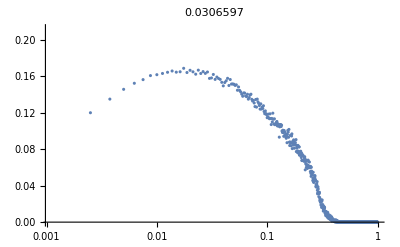

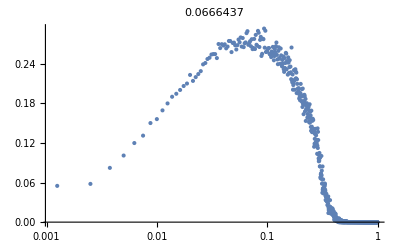

```mathematica
ListLogLinearPlot[QThrustClassicDGLAPQ91test[[2,DaI,2]]/.{a1_,a2_}->{a1,a1 a2},PlotLabel->ToString[SUMRule[QThrustClassicDGLAPQ91test[[2,DaI,2]],1]]]
ListLogLinearPlot[GThrustClassicDGLAPQ91test[[2,DaI,2]]/.{a1_,a2_}->{a1,a1 a2},PlotLabel->ToString[SUMRule[GThrustClassicDGLAPQ91test[[2,DaI,2]],1]]]
```

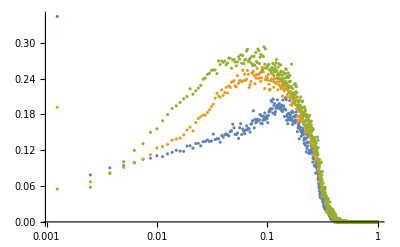

```mathematica
ListLogLinearPlot[{GThrustClassicDGLAPQ91test[[2,3,2]]/.{a1_,a2_}->{a1,a1 a2},GThrustClassicDGLAPQ91test[[2,5,2]]/.{a1_,a2_}->{a1,a1 a2},GThrustClassicDGLAPQ91test[[2,10,2]]/.{a1_,a2_}->{a1,a1 a2}}]
```

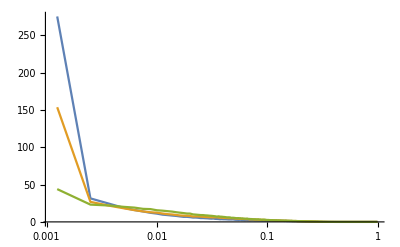

```mathematica
ListLogLinearPlot[{GThrustClassicDGLAPQ91test[[2,3,2]]/.{a1_,a2_}->{a1,a2},GThrustClassicDGLAPQ91test[[2,5,2]]/.{a1_,a2_}->{a1,a2},GThrustClassicDGLAPQ91test[[2,10,2]]/.{a1_,a2_}->{a1, a2}},PlotRange->All,Joined->True]
```

```mathematica
(***************************************************************************************************)
(***************************************************************************************************)
(***************************************************************************************************)
```

```mathematica
(*
The shower conserves the total energy of the jet, and the transverse momentum relative to the parent direction of the daughters given in a splitting. It does not conserve the global transverse momentum with respect to the initiating parton of the shower. The below plots are the average of the square of the sum of the transverse momentum or all partons in the jet relative to the initiating  direction. 
*)
```

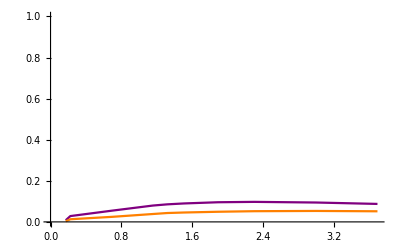

```mathematica
ListPlot[{Table[{GktConserveClassicDGLAPQ91test[[2,i,1]],SUMRuleSpecial[GktConserveClassicDGLAPQ91test[[2,i,2]],1]},{i,1,Length[GktConserveClassicDGLAPQ91test[[2]]]}]/.{a1_,a2_}->{-Log[Tan[a1/2]],a2},Table[{QktConserveClassicDGLAPQ91test[[2,i,1]],SUMRuleSpecial[QktConserveClassicDGLAPQ91test[[2,i,2]],1]},{i,1,Length[QktConserveClassicDGLAPQ91test[[2]]]}]/.{a1_,a2_}->{-Log[Tan[a1/2]],a2}},PlotStyle->PlotStyle1,Joined->True,PlotRange->{0,1}]
```

```mathematica
(***************************************************************************************************)
(***************************************************************************************************)
(***************************************************************************************************)
```

```mathematica
Table[{QktConserveClassicDGLAPQ91test[[2,i,1]],SUMRuleSpecial[QktConserveClassicDGLAPQ91test[[2,i,2]],0]},{i,1,Length[GThrustClassicDGLAPQ91test[[2]]]}]
Table[{GThrustClassicDGLAPQ91test[[2,i,1]],SUMRuleSpecial[GThrustClassicDGLAPQ91test[[2,i,2]],0]},{i,1,Length[GThrustClassicDGLAPQ91test[[2]]]}]
```

{{1.4,1.},{1.34948,1.},{0.927295,1.},{0.610865,1.},{0.523599,1.},{0.436332,1.},{0.3,1.},{0.2,1.},{0.1,1.},{0.05,1.}}

{{1.4,1.},{1.34948,1.},{0.927295,1.},{0.610865,1.},{0.523599,1.},{0.436332,1.},{0.3,1.},{0.2,1.},{0.1,1.},{0.05,1.}}